# Jugando con las muestras del Gran Test 3

```mathematica
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/CoolTools2.m"]
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/usefulFunctions.wl"]
<<"MaTeX`"
```

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/muestras_MH/gran_test_3"]
```

/media/storage/ciencia/investigacion/tesis/muestras_MH/gran_test_3

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/muestras_MH"]
```

/media/storage/ciencia/investigacion/tesis/muestras_MH

```mathematica
(*Función para importar una muestra y obtener su error máximo:*)
importAndGetMeanStd[sampleNum_, targetNum_, swapP_]:= With[{distsample = distsToTarget[Get["sampleMH_"<>ToString[sampleNum]<>".m"][[2]][[6000;;8000]], targets[[targetNum]], swapP]},
													 {Mean[distsample], StandardDeviation[distsample]}];
```

```mathematica
(*función para obtener las posiciones de todas las tuplas de parámetros donde estén involucrados
el target con la swapP indicados en sus argumentos:*)
getParamsPositions[target_, swapP_]:= With[{targetstate=(IdentityMatrix[2]+target PauliMatrix[3])/2},
									  Position[allParams,{_,_,swapP,targetstate},1]]
```

```mathematica
partsδ = {3, 6, 8, 10, 14, 16, 18, 22};
deltas
```

{0.001,0.003,0.005,0.007,0.009,0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085,0.09}

```mathematica
selectionFunc[data_]:= Select[data, MemberQ[deltas[[partsδ]], #[[1]]]&]
```

## Jugando con las muestras obtenidas para r_z = 0

### p = 0.3

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0 y p = 0.3 que se hayan generado:*)
sampleNumsRceroPptoTres = Select[Flatten@getParamsPositions[0, 0.3], ((# < 1153) || (1188 < # < 1283))&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRceroPptoTres = Map[#[[1;;2]]&, allParams[[sampleNumsRceroPptoTres]]];
```

```mathematica
(* Sólo los errores (i.e., promedio) de cada muestra con sus respectivas desviaciones. 
Tiene la siguiente estructura: {{prom1, StdDev1}, {prom2, StdDev2}, ...}*)
errorsRceroPptoTres = Map[importAndGetMeanStd[#, 1, 0.3]&, sampleNumsRceroPptoTres];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ, es decir, puntos tridimensionales (serían en 4D pues se incluyen las desviaciones):*)
errDataRceroPptoTres4D = MapThread[Append[#1, #2]&, {βδValuesRceroPptoTres, errorsRceroPptoTres}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ, con las respectivas desviaciones*)
errDataRceroPptoTres2D = Map[(#[[{1,3}]]&) /@ errDataRceroPptoTres4D[[Flatten[Position[errDataRceroPptoTres4D, {_, #, _}]]]]&, deltas];
errDataRceroPptoTres2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRceroPptoTres2D;
```

```mathematica
(*Datos bidimensionales: error en función de δ, para cada β*)
errDataR0Pp3δ =  Map[(#[[{2,3}]]&) /@ errDataRceroPptoTres4D[[Flatten[Position[errDataRceroPptoTres4D, {#, _, _}]]]]&, betas];
errDataR0Pp3δ =  Map[{#[[1]], #[[2,1]]}&, #]& /@ errDataR0Pp3δ;
errDataR0Pp3δ =  Map[selectionFunc[#]&, errDataR0Pp3δ];
```

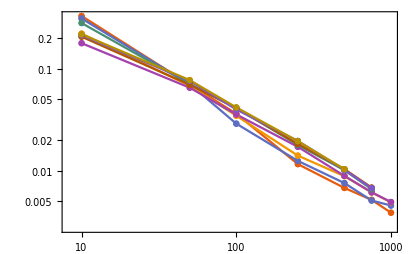
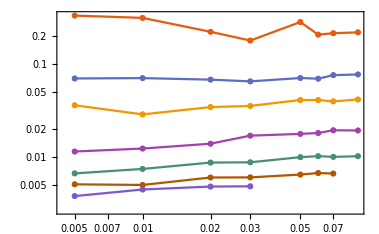

```mathematica
{ListLogLogPlot[errDataRceroPptoTres2D[[partsδ]], 
			   PlotLegends->PointLegend[MaTeX@deltas[[partsδ]], LegendLabel->MaTeX["\\delta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black], 
			   PlotTheme->"Scientific", GridLines->Automatic, 
			   FrameLabel->MaTeX[{"\\text{Estrechez}\\,\\,(\\beta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->Thick],
ListLogLogPlot[errDataR0Pp3δ,
			   PlotLegends->PointLegend[MaTeX@betas, LegendLabel->MaTeX["\\beta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black],
			   PlotTheme->"Scientific", GridLines->Automatic,
			   FrameLabel->MaTeX[{"\\text{Paso}\\,\\,(\\delta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->Thick]
}
```

#### Regresión lineal

```mathematica
(*Regresión de los datos logarítmicos, con todas las deltas juntas*)
lmR0Pp3 = LinearModelFit[Flatten[Log[errDataRceroPptoTres2D[[partsδ]]],1], x, x]
```

FittedModel[0.650611-0.86555 x]

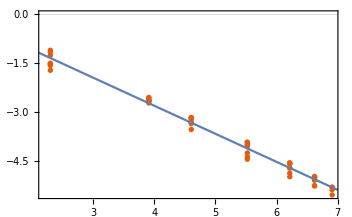
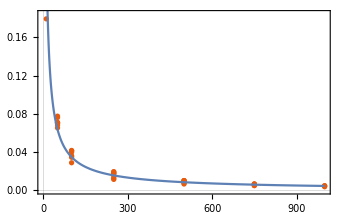
-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 86.7745 | 86.7745 | 3436.01 | 4.82373×10^-47
Error | 49 | 1.23747 | 0.0252544 |  | 
Total | 50 | 88.012 |  |  |  | -Graphics-

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRceroPptoTres2D[[partsδ]]],1], PlotTheme->"Scientific"], Plot[lmR0Pp3[x],{x,0,7}]], lmR0Pp3["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRceroPptoTres2D[[partsδ]],1], PlotTheme->"Scientific"], Plot[Exp[65/100]/x^(87/100), {x, 0,1000}, PlotRange->Full]]}
}]
```

### p = 0.5

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0 y p = 0.5 que se hayan generado:*)
sampleNumsRceroPptoCinco = Select[Flatten@getParamsPositions[0, 0.5], ((# < 1153) || (1188 < # < 1283))&];
```

```mathematica
Grid[{{ListPlot[Log[errDataRceroPptoCinco2D], PlotLegends->deltas, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"ln β", "ln ϵ"}],
	   ListPlot[errDataRceroPptoCinco2D, PlotTheme->"Scientific", GridLines->Automatic, FrameLabel->{"Ancho β", "Error ϵ"}]}
}]
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRceroPptoCinco = Map[#[[1;;2]]&, allParams[[sampleNumsRceroPptoCinco]]];
```

```mathematica
(*Errores máximos de cada muestra:*)
errorsRceroPptoCinco = Map[importAndGetMeanStd[#, 1, 0.5]&, sampleNumsRceroPptoCinco];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ:*)
errDataRceroPptoCinco4D = MapThread[Append[#1, #2]&, {βδValuesRceroPptoCinco, errorsRceroPptoCinco}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ, con las respectivas desviaciones*)
errDataRceroPptoCinco2D = Map[(#[[{1,3}]]&) /@ errDataRceroPptoCinco4D[[Flatten[Position[errDataRceroPptoCinco4D, {_, #, _}]]]]&, deltas];
errDataRceroPptoCinco2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRceroPptoCinco2D;
```

```mathematica
(*Datos bidimensionales: error en función de δ, para cada β*)
errDataR0Pp5δ =  Map[(#[[{2,3}]]&) /@ errDataRceroPptoCinco4D[[Flatten[Position[errDataRceroPptoCinco4D, {#, _, _}]]]]&, betas];
errDataR0Pp5δ =  Map[{#[[1]], #[[2,1]]}&, #]& /@ errDataR0Pp5δ;
errDataR0Pp5δ =  Map[selectionFunc[#]&, errDataR0Pp5δ];
```

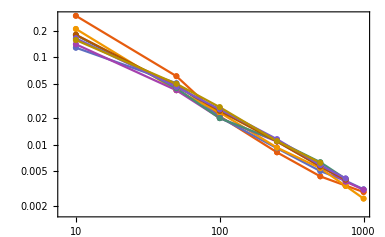
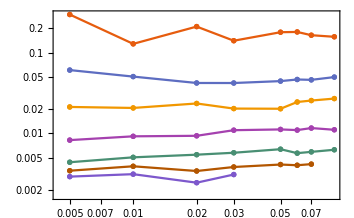

```mathematica
{ListLogLogPlot[errDataRceroPptoCinco2D[[partsδ]], 
			   PlotLegends->PointLegend[MaTeX@deltas[[partsδ]], LegendLabel->MaTeX["\\delta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black], 
			   PlotTheme->"Scientific", GridLines->Automatic, 
			   FrameLabel->MaTeX[{"\\text{Estrechez}\\,\\,(\\beta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->Thick],
ListLogLogPlot[errDataR0Pp5δ,
			   PlotLegends->PointLegend[MaTeX@betas, LegendLabel->MaTeX["\\beta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black],
			   PlotTheme->"Scientific", GridLines->Automatic,
			   FrameLabel->MaTeX[{"\\text{Paso}\\,\\,(\\delta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->Thick]
}
```

#### Regresión lineal

```mathematica
lmR0Pp5 = LinearModelFit[Flatten[Log[errDataRceroPptoCinco2D[[partsδ]]],1], x, x]
```

FittedModel[0.368994-0.896203 x]

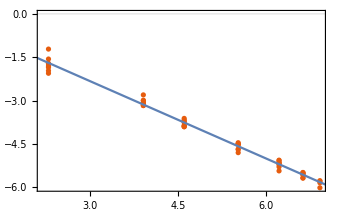
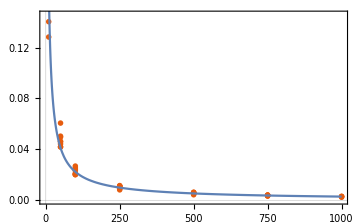
-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 93.0296 | 93.0296 | 4394.71 | 1.25018×10^-49
Error | 49 | 1.03726 | 0.0211685 |  | 
Total | 50 | 94.0669 |  |  |  | -Graphics-

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRceroPptoCinco2D[[partsδ]]],1], PlotTheme->"Scientific"], Plot[lmR0Pp5[x],{x,0,7}]], lmR0Pp5["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRceroPptoCinco2D[[partsδ]],1], PlotTheme->"Scientific"], Plot[Exp[0.2623]/x^(0.8819), {x, 0,1000}, PlotRange->Full]]}
}]
```

### p = 0.8

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0 y p = 0.8 que se hayan generado:*)
sampleNumsRceroPptoOcho = Select[Flatten@getParamsPositions[0, 0.8], ((# < 1153) || (1188 < # < 1283)) && (# != 988)&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRceroPptoOcho = Map[#[[1;;2]]&, allParams[[sampleNumsRceroPptoOcho]]];
```

```mathematica
(*Errores máximos de cada muestra:*)
errorsRceroPptoOcho = Map[importAndGetMeanStd[#, 1, 0.8]&, sampleNumsRceroPptoOcho];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ:*)
errDataRceroPptoOcho4D = MapThread[Append[#1, #2]&, {βδValuesRceroPptoOcho, errorsRceroPptoOcho}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ, con las respectivas desviaciones*)
errDataRceroPptoOcho2D = Map[(#[[{1,3}]]&) /@ errDataRceroPptoOcho4D[[Flatten[Position[errDataRceroPptoOcho4D, {_, #, _}]]]]&, deltas];
errDataRceroPptoOcho2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRceroPptoOcho2D;
```

```mathematica
(*Datos bidimensionales: error en función de δ, para cada β*)
errDataR0Pp8δ =  Map[(#[[{2,3}]]&) /@ errDataRceroPptoOcho4D[[Flatten[Position[errDataRceroPptoOcho4D, {#, _, _}]]]]&, betas];
errDataR0Pp8δ =  Map[{#[[1]], #[[2,1]]}&, #]& /@ errDataR0Pp8δ;
errDataR0Pp8δ =  Map[selectionFunc[#]&, errDataR0Pp8δ];
```

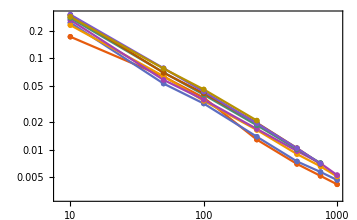
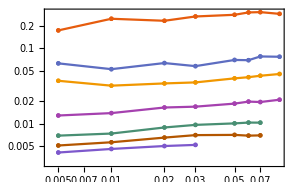

```mathematica
{ListLogLogPlot[errDataRceroPptoOcho2D[[partsδ]], 
			   PlotLegends->PointLegend[MaTeX@deltas[[partsδ]], LegendLabel->MaTeX["\\delta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black], 
			   PlotTheme->"Scientific", GridLines->Automatic, 
			   FrameLabel->MaTeX[{"\\text{Estrechez}\\,\\,(\\beta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->Thick],
ListLogLogPlot[errDataR0Pp8δ,
			   PlotLegends->PointLegend[MaTeX@betas, LegendLabel->MaTeX["\\beta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black],
			   PlotTheme->"Scientific", GridLines->Automatic,
			   FrameLabel->MaTeX[{"\\text{Paso}\\,\\,(\\delta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->Thick]
}
```

```mathematica
Export["numErrorResults_R0Pp8_deltaVSeps.pdf", %115[[2]]]
```

numErrorResults_R0Pp8_deltaVSeps.pdf

#### Regresión lineal

```mathematica
lmR0Pp8 = LinearModelFit[Flatten[Log[errDataRceroPptoOcho2D[[partsδ]]],1], x, x]
```

FittedModel[0.645218-0.859134 x]

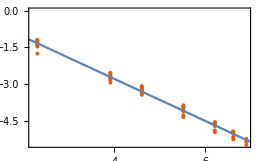
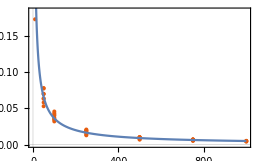
-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 84.3612 | 84.3612 | 3970.18 | 8.21593×10^-48
Error | 48 | 1.01994 | 0.0212487 |  | 
Total | 49 | 85.3812 |  |  |  | -Graphics-

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRceroPptoOcho2D[[partsδ]]],1], PlotTheme->"Scientific"], Plot[lmR0Pp8[x],{x,0,7}]], lmR0Pp8["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRceroPptoOcho2D[[partsδ]],1], PlotTheme->"Scientific"], Plot[Exp[0.64]/x^(0.86), {x, 0,1000}, PlotRange->Full]]}
}]
```

## Jugando con las muestras obtenidas para r_z = 0.5

### p = 0.3

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0.5 y p = 0.3 que se hayan generado:*)
sampleNumsRptoCincoPptoTres = Select[Flatten@getParamsPositions[0.5, 0.3], (# < 1153) || (1188 < # < 1283)&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRptoCincoPptoTres = Map[#[[1;;2]]&, allParams[[sampleNumsRptoCincoPptoTres]]];
```

```mathematica
(*Errores máximos de cada muestra:*)
errorsRptoCincoPptoTres = Map[importAndGetMeanStd[#, 2, 0.3]&, sampleNumsRptoCincoPptoTres];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ:*)
errDataRptoCincoPptoTres4D = MapThread[Append[#1, #2]&, {βδValuesRptoCincoPptoTres, errorsRptoCincoPptoTres}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ*)
errDataRptoCincoPptoTres2D = Map[(#[[{1,3}]]&) /@ errDataRptoCincoPptoTres4D[[Flatten[Position[errDataRptoCincoPptoTres4D, {_, #, _}]]]]&, deltas];
errDataRptoCincoPptoTres2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRptoCincoPptoTres2D;
```

```mathematica
(*Datos bidimensionales: error en función de δ, para cada β*)
errDataRp5Pp3δ =  Map[(#[[{2,3}]]&) /@ errDataRptoCincoPptoTres4D[[Flatten[Position[errDataRptoCincoPptoTres4D, {#, _, _}]]]]&, betas];
errDataRp5Pp3δ =  Map[{#[[1]], #[[2,1]]}&, #]& /@ errDataRp5Pp3δ;
errDataRp5Pp3δ =  Map[selectionFunc[#]&, errDataRp5Pp3δ];
```

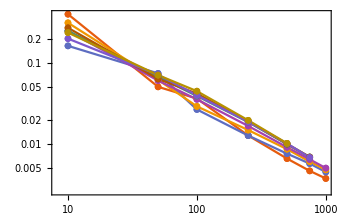
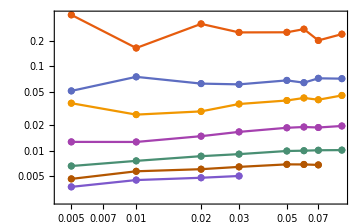

```mathematica
{ListLogLogPlot[errDataRptoCincoPptoTres2D[[partsδ]], 
			   PlotLegends->PointLegend[MaTeX@deltas[[partsδ]], LegendLabel->MaTeX["\\delta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black], 
			   PlotTheme->"Scientific", GridLines->Automatic, 
			   FrameLabel->MaTeX[{"\\text{Estrechez}\\,\\,(\\beta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->PointSize[0.014]],
ListLogLogPlot[errDataRp5Pp3δ,
			   PlotLegends->PointLegend[MaTeX@betas, LegendLabel->MaTeX["\\beta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black],
			   PlotTheme->"Scientific", GridLines->Automatic,
			   FrameLabel->MaTeX[{"\\text{Paso}\\,\\,(\\delta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->PointSize[0.014]]
}
```

```mathematica
Export["numErrorResults_Rp5Pp3_deltaVSeps.pdf", %37[[2]]]
```

numErrorResults_Rp5Pp3_deltaVSeps.pdf

#### Regresión lineal

```mathematica
lmRp5Pp3 = LinearModelFit[Flatten[Log[errDataRptoCincoPptoTres2D[[partsδ]]],1], x, x]
```

FittedModel[0.654039-0.867629 x]

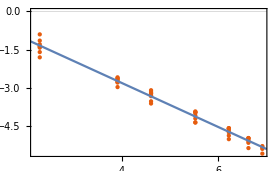
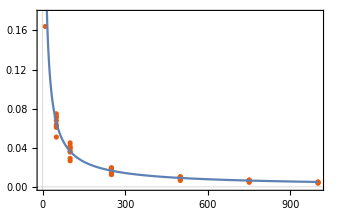
-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 87.192 | 87.192 | 2897.42 | 2.95267×10^-45
Error | 49 | 1.47456 | 0.030093 |  | 
Total | 50 | 88.6665 |  |  |  | -Graphics-

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRptoCincoPptoTres2D[[partsδ]]],1], PlotTheme->"Scientific"], Plot[lmRp5Pp3[x],{x,0,7}]], lmRp5Pp3["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRptoCincoPptoTres2D[[partsδ]],1], PlotTheme->"Scientific"], Plot[Exp[0.646]/x^(0.86), {x, 0,1000}, PlotRange->Full]]}
}]
```

```mathematica
linearmodelTEST = LinearModelFit[Flatten[#[[4;;]]& /@ Log[errDataRptoCincoPptoTres2D[[partsδ]]], 1], x, x]
```

FittedModel[0.969525-0.918624 x]

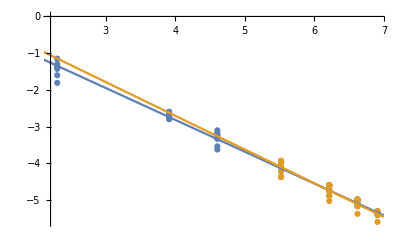

```mathematica
Show[ListPlot[{Flatten[Log[errDataRptoCincoPptoTres2D[[partsδ]]][[2;;]],1],
		  Flatten[#[[4;;]]& /@ Log[errDataRptoCincoPptoTres2D[[partsδ]]], 1]}],
	 Plot[{lmRp5Pp3[x], linearmodelTEST[x]}, {x, 0,7}]
]
```

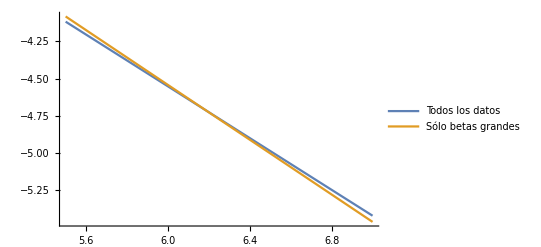
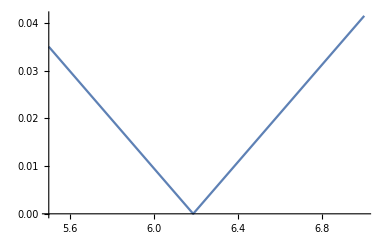

```mathematica
{Plot[{lmRp5Pp3[x], linearmodelTEST[x]}, {x, 5.5,7}, PlotLegends->{"Todos los datos", "Sólo betas grandes"}], Plot[Abs[lmRp5Pp3[x]-linearmodelTEST[x]], {x,5.5,7}]}
```

### p = 0.5

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0.5 y p = 0.5 que se hayan generado:*)
sampleNumsRptoCincoPptoCinco = Select[Flatten@getParamsPositions[0.5, 0.5], (# < 1153) || (1188 < # < 1283)&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRptoCincoPptoCinco = Map[#[[1;;2]]&, allParams[[sampleNumsRptoCincoPptoCinco]]];
```

```mathematica
(*Errores máximos de cada muestra:*)
errorsRptoCincoPptoCinco = Map[importAndGetMeanStd[#, 2, 0.5]&, sampleNumsRptoCincoPptoCinco];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ:*)
errDataRptoCincoPptoCinco4D = MapThread[Append[#1, #2]&, {βδValuesRptoCincoPptoCinco, errorsRptoCincoPptoCinco}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ*)
errDataRptoCincoPptoCinco2D = Map[(#[[{1,3}]]&) /@ errDataRptoCincoPptoCinco4D[[Flatten[Position[errDataRptoCincoPptoCinco4D, {_, #, _}]]]]&, deltas];
errDataRptoCincoPptoCinco2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRptoCincoPptoCinco2D;
```

```mathematica
(*Datos bidimensionales: error en función de δ, para cada β*)
errDataRp5Pp5δ =  Map[(#[[{2,3}]]&) /@ errDataRptoCincoPptoCinco4D[[Flatten[Position[errDataRptoCincoPptoCinco4D, {#, _, _}]]]]&, betas];
errDataRp5Pp5δ =  Map[{#[[1]], #[[2,1]]}&, #]& /@ errDataRp5Pp5δ;
errDataRp5Pp5δ =  Map[selectionFunc[#]&, errDataRp5Pp5δ];
```

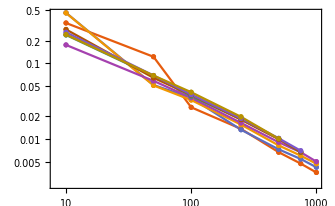
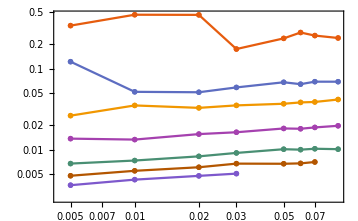

```mathematica
{ListLogLogPlot[errDataRptoCincoPptoCinco2D[[partsδ]], 
			   PlotLegends->PointLegend[MaTeX@deltas[[partsδ]], LegendLabel->MaTeX["\\delta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black], 
			   PlotTheme->"Scientific", GridLines->Automatic, 
			   FrameLabel->MaTeX[{"\\text{Estrechez}\\,\\,(\\beta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->Thick],
ListLogLogPlot[errDataRp5Pp5δ,
			   PlotLegends->PointLegend[MaTeX@betas, LegendLabel->MaTeX["\\beta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black],
			   PlotTheme->"Scientific", GridLines->Automatic,
			   FrameLabel->MaTeX[{"\\text{Paso}\\,\\,(\\delta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->Thick]
}
```

#### Regresión lineal

```mathematica
lmRp5Pp5 = LinearModelFit[Flatten[Log[errDataRptoCincoPptoCinco2D[[partsδ]]],1], x, x]
```

FittedModel[0.806014-0.892465 x]

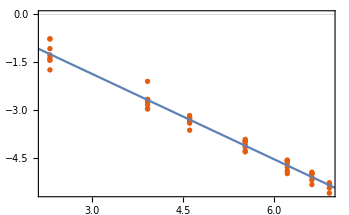
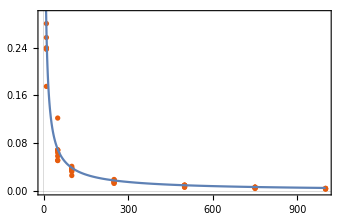
-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 92.2552 | 92.2552 | 2224.77 | 1.69314×10^-42
Error | 49 | 2.0319 | 0.0414673 |  | 
Total | 50 | 94.2871 |  |  |  | -Graphics-

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRptoCincoPptoCinco2D[[partsδ]]],1], PlotTheme->"Scientific"], Plot[lmRp5Pp5[x],{x,0,7}]], lmRp5Pp5["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRptoCincoPptoCinco2D[[partsδ]],1], PlotTheme->"Scientific"], Plot[Exp[0.632]/x^(0.84), {x, 0,1000}, PlotRange->Full]]}
}]
```

### p = 0.8

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0.5 y p = 0.8 que se hayan generado:*)
sampleNumsRptoCincoPptoOcho = Select[Flatten@getParamsPositions[0.5, 0.8], ((# < 1153) || (1188 < # < 1283)) && (# != 989)&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRptoCincoPptoOcho = Map[#[[1;;2]]&, allParams[[sampleNumsRptoCincoPptoOcho]]];
```

```mathematica
(*Errores máximos de cada muestra:*)
errorsRptoCincoPptoOcho = Map[importAndGetMeanStd[#, 2, 0.8]&, sampleNumsRptoCincoPptoOcho];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ:*)
errDataRptoCincoPptoOcho4D = MapThread[Append[#1, #2]&, {βδValuesRptoCincoPptoOcho, errorsRptoCincoPptoOcho}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ, con las respectivas desviaciones*)
errDataRptoCincoPptoOcho2D = Map[(#[[{1,3}]]&) /@ errDataRptoCincoPptoOcho4D[[Flatten[Position[errDataRptoCincoPptoOcho4D, {_, #, _}]]]]&, deltas];
errDataRptoCincoPptoOcho2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRptoCincoPptoOcho2D;
```

```mathematica
(*Datos bidimensionales: error en función de δ, para cada β*)
errDataRp5Pp8δ =  Map[(#[[{2,3}]]&) /@ errDataRptoCincoPptoOcho4D[[Flatten[Position[errDataRptoCincoPptoOcho4D, {#, _, _}]]]]&, betas];
errDataRp5Pp8δ =  Map[{#[[1]], #[[2,1]]}&, #]& /@ errDataRp5Pp8δ;
errDataRp5Pp8δ =  Map[selectionFunc[#]&, errDataRp5Pp8δ];
```

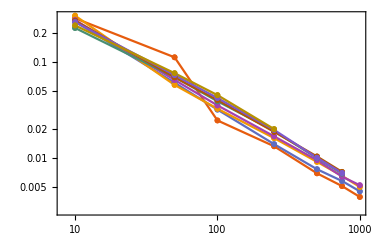
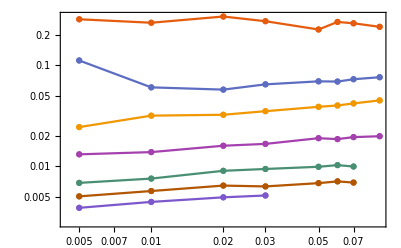

```mathematica
{ListLogLogPlot[errDataRptoCincoPptoOcho2D[[partsδ]], 
			   PlotLegends->PointLegend[MaTeX@deltas[[partsδ]], LegendLabel->MaTeX["\\delta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black], 
			   PlotTheme->"Scientific", GridLines->Automatic, 
			   FrameLabel->MaTeX[{"\\text{Estrechez}\\,\\,(\\beta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->Thick],
ListLogLogPlot[errDataRp5Pp8δ,
			   PlotLegends->PointLegend[MaTeX@betas, LegendLabel->MaTeX["\\beta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black],
			   PlotTheme->"Scientific", GridLines->Automatic,
			   FrameLabel->MaTeX[{"\\text{Paso}\\,\\,(\\delta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->Thick]
}
```

#### Regresión lineal

```mathematica
lmRp5Pp8 = LinearModelFit[Flatten[Log[errDataRptoCincoPptoOcho2D[[partsδ]]],1], x, x]
```

FittedModel[0.726392-0.875572 x]

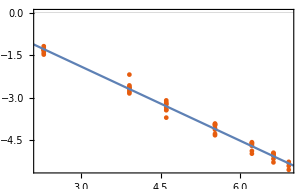
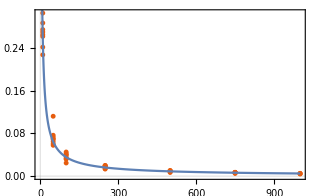
-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 87.6204 | 87.6204 | 3684.3 | 4.83191×10^-47
Error | 48 | 1.14154 | 0.0237821 |  | 
Total | 49 | 88.7619 |  |  |  | -Graphics-

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRptoCincoPptoOcho2D[[partsδ]]],1], PlotTheme->"Scientific"], Plot[lmRp5Pp8[x],{x,0,7}]], lmRp5Pp8["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRptoCincoPptoOcho2D[[partsδ]],1], PlotTheme->"Scientific"], Plot[Exp[0.63]/x^(0.862), {x, 0,1000}, PlotRange->Full]]}
}]
```

## Jugando con las muestras obtenidas para r_z = 0.8

### p = 0.3

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0.8 y p = 0.3 que se hayan generado:*)
sampleNumsRptoOchoPptoTres = Select[Flatten@getParamsPositions[0.8, 0.3], ((# < 1153) || (1188 < # < 1283))&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRptoOchoPptoTres = Map[#[[1;;2]]&, allParams[[sampleNumsRptoOchoPptoTres]]];
```

```mathematica
(*Errores máximos de cada muestra:*)
errorsRptoOchoPptoTres = Map[importAndGetMeanStd[#, 3, 0.3]&, sampleNumsRptoOchoPptoTres];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ:*)
errDataRptoOchoPptoTres4D = MapThread[Append[#1, #2]&, {βδValuesRptoOchoPptoTres, errorsRptoOchoPptoTres}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ, con las respectivas desviaciones*)
errDataRptoOchoPptoTres2D = Map[(#[[{1,3}]]&) /@ errDataRptoOchoPptoTres4D[[Flatten[Position[errDataRptoOchoPptoTres4D, {_, #, _}]]]]&, deltas];
errDataRptoOchoPptoTres2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRptoOchoPptoTres2D;
```

```mathematica
(*Datos bidimensionales: error en función de δ, para cada β*)
errDataRp8Pp3δ =  Map[(#[[{2,3}]]&) /@ errDataRptoOchoPptoTres4D[[Flatten[Position[errDataRptoOchoPptoTres4D, {#, _, _}]]]]&, betas];
errDataRp8Pp3δ =  Map[{#[[1]], #[[2,1]]}&, #]& /@ errDataRp8Pp3δ;
errDataRp8Pp3δ =  Map[selectionFunc[#]&, errDataRp8Pp3δ];
```

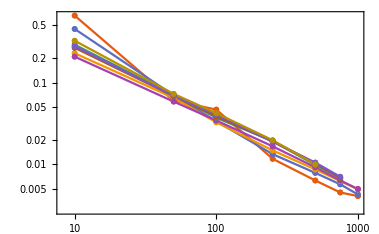
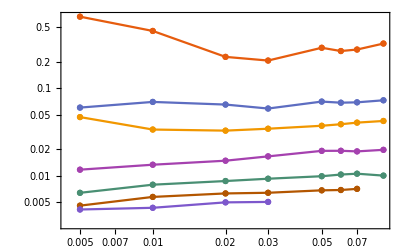

```mathematica
{ListLogLogPlot[errDataRptoOchoPptoTres2D[[partsδ]], 
			   PlotLegends->PointLegend[MaTeX@deltas[[partsδ]], LegendLabel->MaTeX["\\delta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black], 
			   PlotTheme->"Scientific", GridLines->Automatic, 
			   FrameLabel->MaTeX[{"\\text{Estrechez}\\,\\,(\\beta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->Thick],
ListLogLogPlot[errDataRp8Pp3δ,
			   PlotLegends->PointLegend[MaTeX@betas, LegendLabel->MaTeX["\\beta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black],
			   PlotTheme->"Scientific", GridLines->Automatic,
			   FrameLabel->MaTeX[{"\\text{Paso}\\,\\,(\\delta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->Thick]
}
```

#### Regresión lineal

```mathematica
lmRp8Pp3 = LinearModelFit[Flatten[Log[errDataRptoOchoPptoTres2D[[partsδ]]],1], x, x]
```

FittedModel[0.898034-0.9061 x]

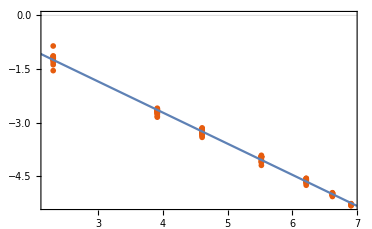
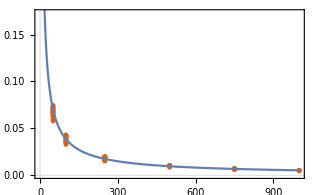
-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 149.029 | 149.029 | 18609.7 | 3.37334×10^-104
Error | 88 | 0.704716 | 0.00800813 |  | 
Total | 89 | 149.733 |  |  |  | -Graphics-

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRptoOchoPptoTres2D],1], PlotTheme->"Scientific"], Plot[lmRp8Pp3[x],{x,0,7}]], lmRp8Pp3["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRptoOchoPptoTres2D,1], PlotTheme->"Scientific"], Plot[Exp[0.75]/x^(0.87), {x, 0,1000}, PlotRange->Full]]}
}]
```

### p = 0.5

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0.8 y p = 0.5 que se hayan generado:*)
sampleNumsRptoOchoPptoCinco = Select[Flatten@getParamsPositions[0.8, 0.5], ((# < 1153) || (1188 < # < 1283))&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRptoOchoPptoCinco = Map[#[[1;;2]]&, allParams[[sampleNumsRptoOchoPptoCinco]]];
```

```mathematica
(*Errores máximos de cada muestra:*)
errorsRptoOchoPptoCinco = Map[importAndGetMeanStd[#, 3, 0.5]&, sampleNumsRptoOchoPptoCinco];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ:*)
errDataRptoOchoPptoCinco4D = MapThread[Append[#1, #2]&, {βδValuesRptoOchoPptoCinco, errorsRptoOchoPptoCinco}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ*)
errDataRptoOchoPptoCinco2D = Map[(#[[{1,3}]]&) /@ errDataRptoOchoPptoCinco4D[[Flatten[Position[errDataRptoOchoPptoCinco4D, {_, #, _}]]]]&, deltas];
errDataRptoOchoPptoCinco2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRptoOchoPptoCinco2D;
```

```mathematica
(*Datos bidimensionales: error en función de δ, para cada β*)
errDataRp8Pp5δ =  Map[(#[[{2,3}]]&) /@ errDataRptoOchoPptoCinco4D[[Flatten[Position[errDataRptoOchoPptoCinco4D, {#, _, _}]]]]&, betas];
errDataRp8Pp5δ =  Map[{#[[1]], #[[2,1]]}&, #]& /@ errDataRp8Pp5δ;
errDataRp8Pp5δ =  Map[selectionFunc[#]&, errDataRp8Pp5δ];
```

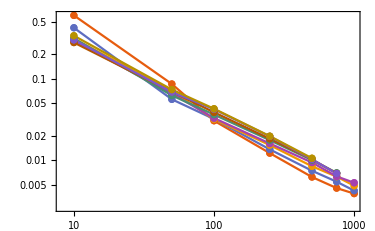
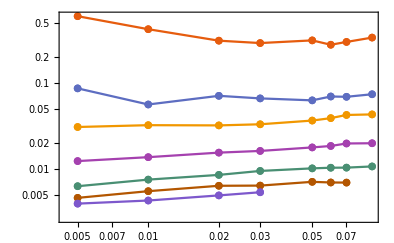

```mathematica
{ListLogLogPlot[errDataRptoOchoPptoCinco2D[[partsδ]], 
			   PlotLegends->PointLegend[MaTeX@deltas[[partsδ]], LegendLabel->MaTeX["\\delta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black], 
			   PlotTheme->"Scientific", GridLines->Automatic, 
			   FrameLabel->MaTeX[{"\\text{Estrechez}\\,\\,(\\beta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->PointSize[0.014]],
ListLogLogPlot[errDataRp8Pp5δ,
			   PlotLegends->PointLegend[MaTeX@betas, LegendLabel->MaTeX["\\beta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black],
			   PlotTheme->"Scientific", GridLines->Automatic,
			   FrameLabel->MaTeX[{"\\text{Paso}\\,\\,(\\delta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->PointSize[0.014]]
}
```

#### Regresión lineal

```mathematica
lmRp8Pp5 = LinearModelFit[Flatten[Log[errDataRptoOchoPptoCinco2D[[partsδ]]],1], x, x]
```

FittedModel[0.9999-0.924858 x]

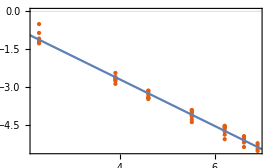
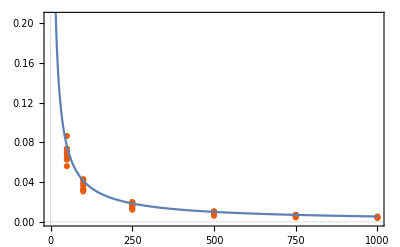
-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 99.0737 | 99.0737 | 3279.72 | 1.485×10^-46
Error | 49 | 1.48019 | 0.030208 |  | 
Total | 50 | 100.554 |  |  |  | -Graphics-

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRptoOchoPptoCinco2D[[partsδ]]],1], PlotTheme->"Scientific"], Plot[lmRp8Pp5[x],{x,0,7}]], lmRp8Pp5["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRptoOchoPptoCinco2D[[partsδ]],1], PlotTheme->"Scientific"], Plot[Exp[0.87]/x^(0.88), {x, 0,1000}, PlotRange->Full]]}
}]
```

### p = 0.8

#### Graficación de los datos

```mathematica
(*Obtenemos los números que identifican a las muestras con rz= 0.8 y p = 0.8 que se hayan generado:*)
sampleNumsRptoOchoPptoOcho = Select[Flatten@getParamsPositions[0.8, 0.8], ((# < 1153) || (1188 < # < 1283)) && (# != 990)&];
```

```mathematica
(*Para esas muestras obtenemos sus valores de β y δ correspondientes:*)
βδValuesRptoOchoPptoOcho = Map[#[[1;;2]]&, allParams[[sampleNumsRptoOchoPptoOcho]]];
```

```mathematica
(*Errores máximos de cada muestra:*)
errorsRptoOchoPptoOcho = Map[importAndGetMeanStd[#, 3, 0.8]&, sampleNumsRptoOchoPptoOcho];
```

```mathematica
(*Juntamos los datos de los errores con sus respectivos valores de β y δ:*)
errDataRptoOchoPptoOcho4D = MapThread[Append[#1, #2]&, {βδValuesRptoOchoPptoOcho, errorsRptoOchoPptoOcho}];
```

```mathematica
(*Datos bidimensionales: error en función de β, para cada δ*)
errDataRptoOchoPptoOcho2D = Map[(#[[{1,3}]]&) /@ errDataRptoOchoPptoOcho4D[[Flatten[Position[errDataRptoOchoPptoOcho4D, {_, #, _}]]]]&, deltas];
errDataRptoOchoPptoOcho2D = Map[{#[[1]], #[[2]][[1]]}&, #]& /@ errDataRptoOchoPptoOcho2D;
```

```mathematica
(*Datos bidimensionales: error en función de δ, para cada β*)
errDataRp8Pp8δ =  Map[(#[[{2,3}]]&) /@ errDataRptoOchoPptoOcho4D[[Flatten[Position[errDataRptoOchoPptoOcho4D, {#, _, _}]]]]&, betas];
errDataRp8Pp8δ =  Map[{#[[1]], #[[2,1]]}&, #]& /@ errDataRp8Pp8δ;
errDataRp8Pp8δ =  Map[selectionFunc[#]&, errDataRp8Pp8δ];
```

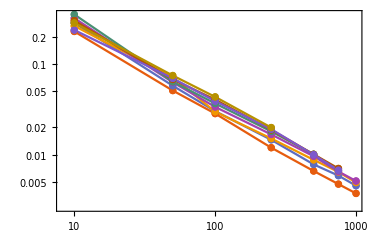
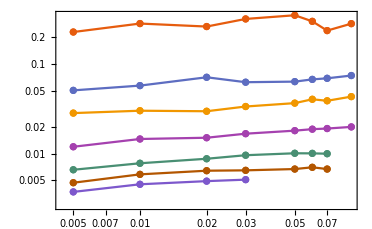

```mathematica
{ListLogLogPlot[errDataRptoOchoPptoOcho2D[[partsδ]], 
			   PlotLegends->PointLegend[MaTeX@deltas[[partsδ]], LegendLabel->MaTeX["\\delta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black], 
			   PlotTheme->"Scientific", GridLines->Automatic, 
			   FrameLabel->MaTeX[{"\\text{Estrechez}\\,\\,(\\beta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->PointSize[0.014]],
ListLogLogPlot[errDataRp8Pp8δ,
			   PlotLegends->PointLegend[MaTeX@betas, LegendLabel->MaTeX["\\beta", Preamble->{"\\usepackage{newtxmath}"}], LabelStyle->Black],
			   PlotTheme->"Scientific", GridLines->Automatic,
			   FrameLabel->MaTeX[{"\\text{Paso}\\,\\,(\\delta)", "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}],
			   FrameStyle->Black,
			   Joined->True, Mesh->Full, MeshStyle->PointSize[0.014]]
}
```

#### Regresión lineal

```mathematica
lmRp8Pp8 = LinearModelFit[Flatten[Log[errDataRptoOchoPptoOcho2D[[partsδ]]],1], x, x]
```

FittedModel[0.744944-0.882696 x]

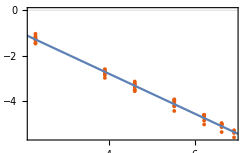
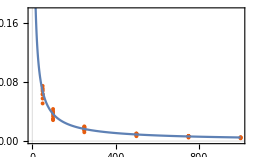
-Graphics- |  | DF | SS | MS | F-Statistic | P-Value
x | 1 | 89.0519 | 89.0519 | 4222.43 | 1.90498×10^-48
Error | 48 | 1.01233 | 0.0210902 |  | 
Total | 49 | 90.0643 |  |  |  | -Graphics-

```mathematica
Grid[{{Show[ListPlot[Flatten[Log[errDataRptoOchoPptoOcho2D[[partsδ]]],1], PlotTheme->"Scientific"], Plot[lmRp8Pp8[x],{x,0,7}]], lmRp8Pp8["ANOVATable"],
	   Show[ListPlot[Flatten[errDataRptoOchoPptoOcho2D[[partsδ]],1], PlotTheme->"Scientific"], Plot[Exp[0.75]/x^(0.88), {x, 0,1000}, PlotRange->Full]]}
}]
```

## Graficando los exponentes

```mathematica
dataR0 = MapThread[{#1, #2}&, {swapPs, {0.86555, 0.896203, 0.859134}}];
dataRp5 = MapThread[{#1, #2}&, {swapPs, {0.867629, 0.892465, 0.875572}}];
dataRp8 = MapThread[{#1, #2}&, {swapPs, {0.9061, 0.924858, 0.882696}}];
```

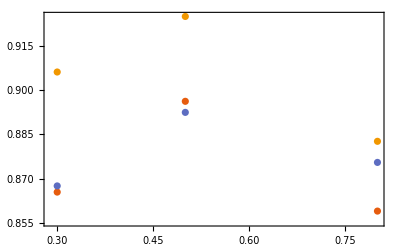

```mathematica
ListPlot[{dataR0, dataRp5, dataRp8}, PlotTheme->"Scientific", PlotLegends->PointLegend[rzs, LegendLabel->MaTeX["r_z"]]]
```

## Comentarios

Al observar estas primeras gráficas, se nota a primera vista que las muestras con δ = 0.001 se comportan distinto a todas las demás (de manera algo extraña). Esto sucede para casi todos los targets y swapPs. El comportamiento extraño consiste en que la desviación de cada error puede llegar a ser enorme, lo que significa que las distancias al target de dichas muestras se alejan mucho de la media. Además, al graficar los errores en función de β en escala Log-Log, no se observa la recta como sí se ve para los demás valores de δ. 

Veamos rápidamente la gráfica distancias de algunos de estos casos extraños.

```mathematica
(*Para rz = 0.5, p = 0.3.*)
testingSamples = Get["sampleMH_"<>ToString[#]<>".m"][[2]][[5001;;8000]]& /@ Flatten@Position[allParams, {_, 0.001, 0.3, targets[[2]]}];
```

```mathematica
sampleDists = distsToTarget[#, targets[[2]], 0.3]& /@ testingSamples;
```

```mathematica
sampleDistsMeans = Mean[#]& /@ sampleDists;
sampleDistsStdPlus = MapThread[(#1 + #2)&, {sampleDistsMeans, Map[StandardDeviation, sampleDists]}];
sampleDistsStdMinus = MapThread[(#1 - #2)&, {sampleDistsMeans, Map[StandardDeviation, sampleDists]}];
```

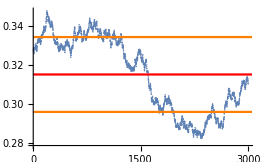
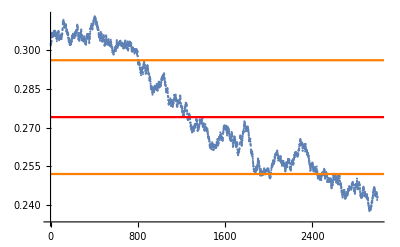
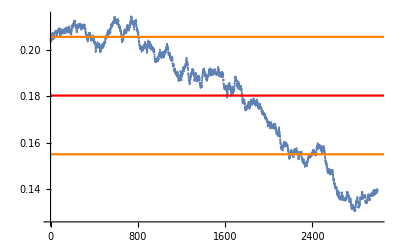
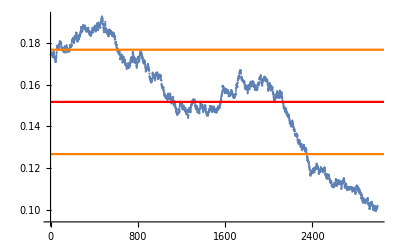
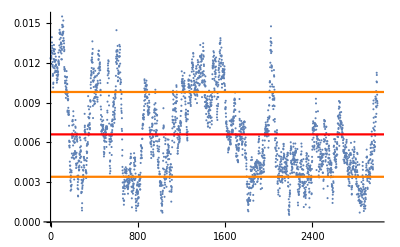
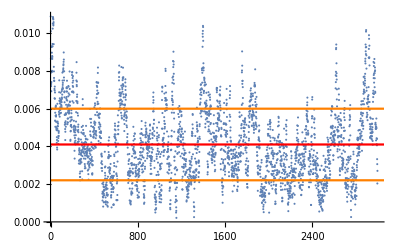
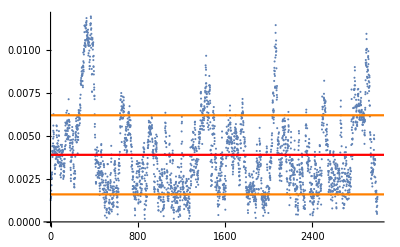

```mathematica
plots = MapThread[Show[ListPlot[#1], Plot[#2,{x,0,4000}, PlotStyle->Red], Plot[{#3, #4},{x,0,4000}, PlotStyle->Orange]]&, 
		  {sampleDists, sampleDistsMeans, sampleDistsStdPlus, sampleDistsStdMinus}]
```

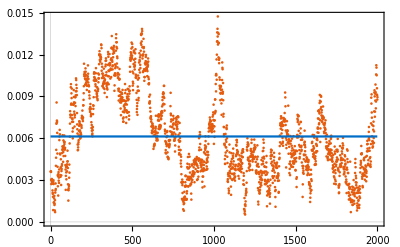

```mathematica
Show[ListPlot[sampleDists[[5]][[1000;;3000]], PlotTheme->"Scientific", FrameLabel->MaTeX[{"\\ket{\\psi_i}\,(i-\\text{ésima iteración})", "d(\\mathcal{C}[\\ket{\\psi_i}], \\varrho_t)"}, Preamble->{"\\usepackage{physics, newtxmath}"}], 
			  FrameStyle->Black], 
	 Plot[Mean[sampleDists[[5]][[1000;;3000]]],{x,0,2000}, PlotStyle->Directive[RGBColor[0.,0.43,0.78]], 
	      PlotLegends->Placed[LineLegend[{MaTeX["\\text{Error}"]}, LegendFunction->(Framed[#1, FrameMargins -> 0] & )], {0.8, 0.85}]]]
```

```mathematica
Export["mh_error_def2.pdf",%65]
```

mh_error_def2.pdf

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis"]
```

/media/storage/ciencia/investigacion/tesis

```mathematica
Length[sampleDists[[5]]]
```

3000

```mathematica
sampleDistsStdMinus (*tomando a partir de la muestra 3000*)
```

{0.285405,0.268588,0.182306,0.14792,-0.00387928,-0.00400041,-0.0209453}

```mathematica
sampleDistsStdMinus (*tomando a partir de la muestra 5000*)
```

{0.295818,0.251964,0.155025,0.126602,0.00340088,0.00220298,0.00160218}

Parece que el comportamiento extraño puede corregirse al tomar elementos de la muestra más cercanos al final, esto es, más “termalizados”. Si no nos deshacemos bien del burn-in no tendremos el error correcto.